Variables

```mathematica
g=9.81;
l = 5;
poc=1;
time = {t, 0, 25};
init = {y[0] == poc, y'[0] == 0};
rovnice = y''[t] + g/l *Sin[y[t]] == 0;
```

--------------------------------------------------------------------------------------------------------------------Ukol(1)--------------------------------------------------------------------------------------------------------------------

```mathematica
Series[1/(1-x)^(1/2),{x,0,10}]
```

1+x/2+(3 x^2)/8+(5 x^3)/16+(35 x^4)/128+(63 x^5)/256+(231 x^6)/1024+(429 x^7)/2048+(6435 x^8)/32768+(12155 x^9)/65536+(46189 x^10)/262144+O[x]^11

```mathematica
k = θ/2;
```

```mathematica
f[x_]:=1+x/2+(3 x^2)/8;
ff[x_] := f[x^2]
```

```mathematica
ff[k*Sin[ϕ]]
```

1+1/8 θ^2 Sin[ϕ]^2+3/128 θ^4 Sin[ϕ]^4

```mathematica
Integrate[ff[k*Sin[ϕ]],{ϕ,0,Pi/2}]
```

(π (1024+64 θ^2+9 θ^4))/2048

```mathematica
Perioda[θ_] := (π (1024+64 θ^2+9 θ^4))/2048*4*Sqrt[l/g]
```

```mathematica
2 π ((9 θ^4)/1024+θ^2/16+1) √(l/g)// TeXForm
```

4.4857 \left(\frac{9 \theta ^4}{1024}+\frac{\theta ^2}{16}+1\right)

--------------------------------------------------------------------------------------------------------------------(0-primou integraci)--------------------------------------------------------------------------------------------------------------------

```mathematica
Elip[θ_]:=Integrate[4*Sqrt[l/g]*1/Sqrt[1-Sin[θ/2]^2*Sin[y]^2],{y,0,Pi/2}]
```

--------------------------------------------------------------------------------------------------------------------Ukol(2)--------------------------------------------------------------------------------------------------------------------

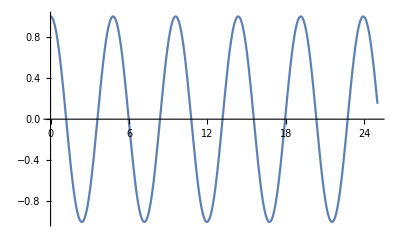

```mathematica
list={};
sol:=NDSolve[{rovnice, init, WhenEvent[y[t] == 0, AppendTo[list,t]]}, y, time]
Plot[Evaluate[y[t] /. sol], time]
```

Porovnani:

```mathematica
Grid[{{"MathematicaDSolve","AproxPeriod","ElipIntegruj","SymplecticPartitionedRungeKutta","ProjectionExplicitRungeKutta","PokazEuler"},{First[list]*4,Perioda[poc],N[Elip[poc]],First[pruchod]*4,First[list3]*4,First[listEU]*4}},Frame->All]
```

MathematicaDSolve | AproxPeriod | ElipIntegruj | SymplecticPartitionedRungeKutta | ProjectionExplicitRungeKutta | PokazEuler
4.78326 | 4.80548 | 4.78326 | 4.7827 | 4.78326 | 4.84121

--------------------------------------------------------------------------------------------------------------------Ukol(3)--------------------------------------------------------------------------------------------------------------------

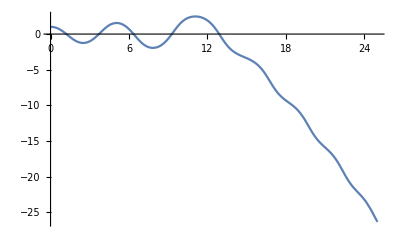

```mathematica
listEU={};
sol2:=NDSolve[{rovnice, init, WhenEvent[y[t] == 0, AppendTo[listEU,t]]}, y, time,Method->"ExplicitEuler",StartingStepSize->0.1,MaxStepSize->0.1,MaxSteps->250]
Plot[Evaluate[y[t]  /. sol2], time]
```

--------------------------------------------------------------------------------------------------------------------Ukol(4)--------------------------------------------------------------------------------------------------------------------

```mathematica
energie=1/2 *(y'[t])^2-g/l *Cos[y[t]];
energie0=-g/l *Cos[poc]
```

-1.06007

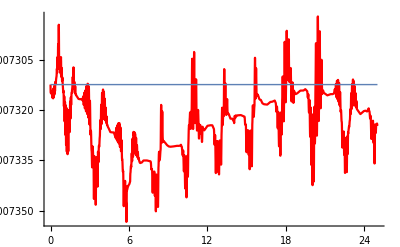

```mathematica
p1=Plot[Evaluate[energie/. sol], time,PlotStyle->Red] ;
p2 = Plot[energie0,time, PlotStyle->Thick];
Show[p1,p2,PlotRange->All]
```

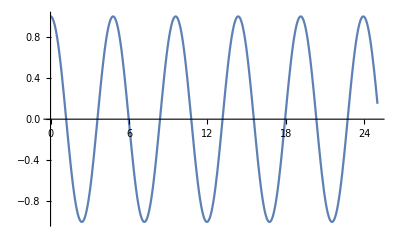

```mathematica
list3={};
sol3I:=NDSolve[{rovnice, init, WhenEvent[y[t] == 0, AppendTo[list3,t]]}, y, time, Method->{"Projection",Method->"ExplicitRungeKutta","Invariants"->energie0}]
Plot[Evaluate[y[t] /. sol3I], time]
```

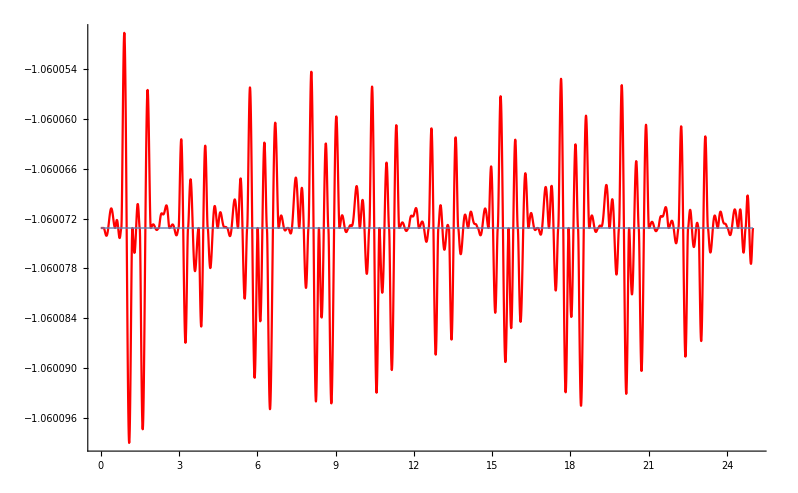

```mathematica
p1=Plot[Evaluate[energie/. sol3I], time,PlotStyle->Red] ;
p2 = Plot[energie0,time, PlotStyle->Thick];
Show[p1,p2,PlotRange->All]
```

--------------------------------------------------------------------------------------------------------------------SympleticPartionedRungeKutta--------------------------------------------------------------------------------------------------------------------
ve druhem 2pendulum.nb

```mathematica
H = p[t]^2/2 -g/l *Cos[q[t]];
eqs = {p'[t] == -D[H, q[t]], q'[t] == D[H, p[t]]};
ics = {p[0] == 0,q[0] == poc};
vars = {q[t], p[t]};
step = 1/25;
pruchod = {};
```

```mathematica
rese=NDSolve[{eqs,ics, WhenEvent[q[t] == 0, AppendTo[pruchod,t]]},vars,time,Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->{q[t]}},StartingStepSize->step, MaxSteps->Infinity];
```

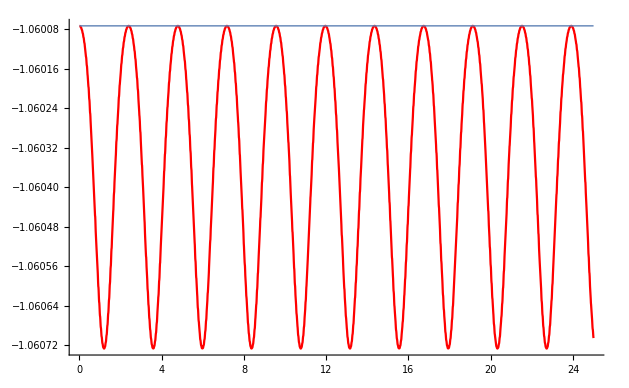

```mathematica
p1=Plot[Evaluate[p[t]^2/2 -g/l *Cos[q[t]]/.rese], time,PlotStyle->Red] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick];
Show[p1,p2,PlotRange->All]
```

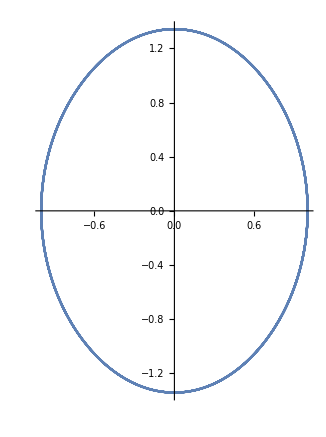

```mathematica
ParametricPlot[Evaluate[vars/. rese],Evaluate[time]]
```

```mathematica
reseeu=NDSolve[{eqs,ics},vars,time,Method->"ExplicitEuler",StartingStepSize->step,MaxSteps->Infinity];
```

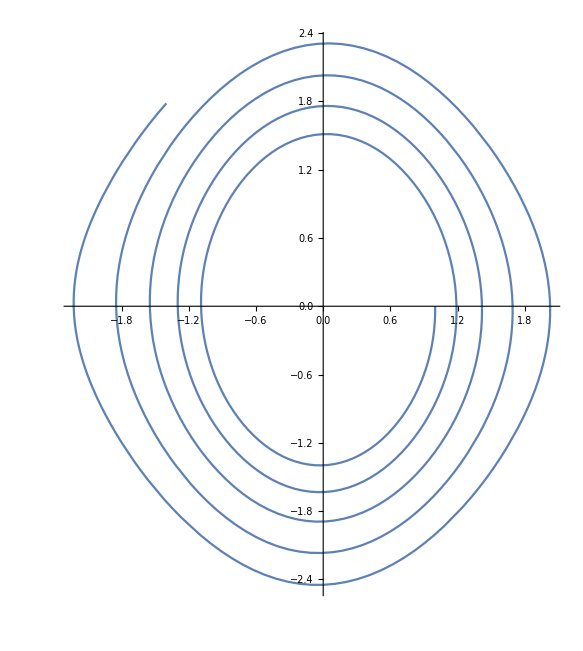

```mathematica
ParametricPlot[Evaluate[vars/. reseeu],Evaluate[time],PlotPoints->10]
```

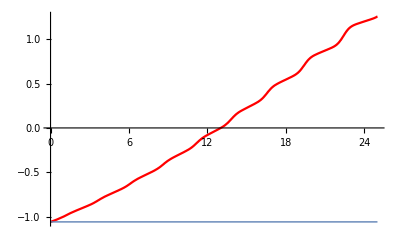

```mathematica
p1=Plot[Evaluate[p[t]^2/2 -g/l *Cos[q[t]]/. reseeu], time,PlotStyle->Red] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick];
Show[p1,p2,PlotRange->All]
```

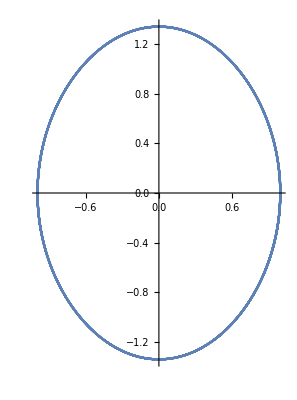

```mathematica
sol3E:=NDSolve[{y''[t] + g/l *Sin[y[t]] == 0, y[0] == poc, y'[0] == 0}, y, time,Method->{"Projection",Method->"ExplicitRungeKutta","Invariants"->-g/l *Cos[poc]},StartingStepSize->step,MaxSteps->Infinity]
ParametricPlot[Evaluate[{y[t], y'[t]}/. sol3E],Evaluate[time]]
```

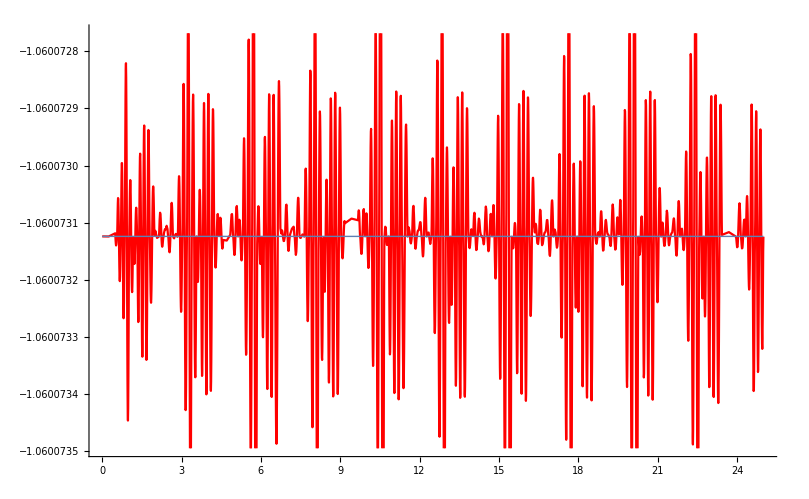

```mathematica
p1=Plot[Evaluate[1/2 *(y'[t])^2-g/l *Cos[y[t]]/. sol3E], time,PlotStyle->Red] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick];
Show[p1,p2,PlotRange->All]
```

--------------------------------------------------------------------------------------------------------------------Ukol(5+6)--------------------------------------------------------------------------------------------------------------------

```mathematica
ϕ[t_]:=ϵ*A[t]+ϵ^3*B[t]+ϵ^5*C[t];
ω^2=O^2+ϵ^2*α+ϵ^4*β+ϵ^6*γ;
```

Set::write: Tag Power in ω^2 is Protected.

```mathematica
Series[Sin[x],{x,0,3}]
```

x-x^3/6+O[x]^4

```mathematica
(ϵ*A''[t]+ϵ^3*B''[t]+ϵ^5*C̈́''[t])+(ω^2-ϵ^2*α-ϵ^4*β-ϵ^6*γ)*(ϵ*A[t]+ϵ^3*B[t]+ϵ^5*C[t]-((ϵ*A[t]+ϵ^3*B[t]+ϵ^5*C[t])^3)/6);
```

```mathematica
Collect[(ϵ*A''[t]+ϵ^3*B''[t]+ϵ^5*C̈́''[t])+(ω^2-ϵ^2*α-ϵ^4*β-ϵ^6*γ)*(ϵ*A[t]+ϵ^3*B[t]+ϵ^5*C[t]-((ϵ*A[t]+ϵ^3*B[t]+ϵ^5*C[t])^3)/6),ϵ]
```

1/6 γ ϵ^21 C[t]^3+ϵ^19 (-(23 ω^2 C[t]^3)/9216+1/384 γ C[t]^2 (-Cos[t ω]+Cos[3 t ω]))+ϵ^17 (-1/48 ω^2 C[t]^3+1/2 γ C[t]^2 Cos[t ω]-(23 ω^2 C[t]^2 (-Cos[t ω]+Cos[3 t ω]))/589824+(γ C[t] (-Cos[t ω]+Cos[3 t ω])^2)/73728)+ϵ^7 ((ω^2 C[t])/8-γ Cos[t ω]-1/2 ω^2 C[t] Cos[t ω]^2-(23 ω^2 Cos[t ω]^3)/9216+(23 ω^2 (-Cos[t ω]+Cos[3 t ω]))/294912-(ω^2 Cos[t ω]^2 (-Cos[t ω]+Cos[3 t ω]))/3072-(ω^2 Cos[t ω] (-Cos[t ω]+Cos[3 t ω])^2)/73728)+ϵ^15 (-1/6 ω^2 C[t]^3-(23 ω^2 C[t]^2 Cos[t ω])/3072-(ω^2 C[t]^2 (-Cos[t ω]+Cos[3 t ω]))/3072+1/192 γ C[t] Cos[t ω] (-Cos[t ω]+Cos[3 t ω])-(23 ω^2 C[t] (-Cos[t ω]+Cos[3 t ω])^2)/113246208+(γ (-Cos[t ω]+Cos[3 t ω])^3)/42467328)+ϵ^9 ((23 ω^2 C[t])/1536-1/16 ω^2 C[t] Cos[t ω]^2+1/6 γ Cos[t ω]^3-1/192 γ (-Cos[t ω]+Cos[3 t ω])-1/192 ω^2 C[t] Cos[t ω] (-Cos[t ω]+Cos[3 t ω])-(23 ω^2 Cos[t ω]^2 (-Cos[t ω]+Cos[3 t ω]))/589824-(ω^2 Cos[t ω] (-Cos[t ω]+Cos[3 t ω])^2)/589824-(ω^2 (-Cos[t ω]+Cos[3 t ω])^3)/42467328)+ϵ^11 (-γ C[t]-1/2 ω^2 C[t]^2 Cos[t ω]-(23 ω^2 C[t] Cos[t ω]^2)/3072-(ω^2 C[t] Cos[t ω] (-Cos[t ω]+Cos[3 t ω]))/1536+1/384 γ Cos[t ω]^2 (-Cos[t ω]+Cos[3 t ω])-(ω^2 C[t] (-Cos[t ω]+Cos[3 t ω])^2)/73728-(23 ω^2 Cos[t ω] (-Cos[t ω]+Cos[3 t ω])^2)/113246208-(ω^2 (-Cos[t ω]+Cos[3 t ω])^3)/339738624)+ϵ^13 (-1/16 ω^2 C[t]^2 Cos[t ω]+1/2 γ C[t] Cos[t ω]^2-1/384 ω^2 C[t]^2 (-Cos[t ω]+Cos[3 t ω])-(23 ω^2 C[t] Cos[t ω] (-Cos[t ω]+Cos[3 t ω]))/294912-(ω^2 C[t] (-Cos[t ω]+Cos[3 t ω])^2)/589824+(γ Cos[t ω] (-Cos[t ω]+Cos[3 t ω])^2)/73728-(23 ω^2 (-Cos[t ω]+Cos[3 t ω])^3)/65229815808)+ϵ (ω^2 Cos[t ω]+A''[t])+ϵ^3 (1/8 ω^2 Cos[t ω]-1/6 ω^2 Cos[t ω]^3+1/192 ω^2 (-Cos[t ω]+Cos[3 t ω])+B''[t])+ϵ^5 (ω^2 C[t]+(23 ω^2 Cos[t ω])/1536-1/48 ω^2 Cos[t ω]^3+(ω^2 (-Cos[t ω]+Cos[3 t ω]))/1536-1/384 ω^2 Cos[t ω]^2 (-Cos[t ω]+Cos[3 t ω])+C̈́''[t])

eps1:  ω^2 A[t]+A''[t]=0
eps3: -α A[t]-1/6 ω^2 A[t]^3+ω^2 B[t]+B''[t]=0
eps5: -β A[t]+1/6 α A[t]^3-α B[t]-1/2 ω^2 A[t]^2 B[t]+ω^2 C[t]+C̈́''[t]=0

```mathematica
A[t]=poc*Cos[ω*t];
B[t]=poc^3/192*(Cos[3*ω*t]-Cos[ω*t]);
α =-(ω^2*poc^2)/8;
```

```mathematica
-β A[t]+1/6 α A[t]^3-α B[t]-1/2 ω^2 A[t]^2 B[t]+ω^2 C[t]+C̈́''[t]
```

ω^2 C[t]+(23 ω^2 Cos[t ω])/1536-1/48 ω^2 Cos[t ω]^3+(ω^2 (-Cos[t ω]+Cos[3 t ω]))/1536-1/384 ω^2 Cos[t ω]^2 (-Cos[t ω]+Cos[3 t ω])+C̈́''[t]

C -> y

```mathematica
y''[t]+ω^2 *y[t]==+poc β Cos[t ω]-1/6 poc^3 α Cos[t ω]^3+1/192 poc^3 α (-Cos[t ω]+Cos[3 t ω])+1/384 poc^5 ω^2 Cos[t ω]^2 (-Cos[t ω]+Cos[3 t ω])//TrigReduce
```

ω^2 y[t]+y''[t]==(8 ω^2 Cos[3 t ω]+ω^2 Cos[5 t ω])/1536

```mathematica
Solve[1536 poc β +23 poc^5 ω^2 ==0,β]
```

Solve::ivar: -(23 ω^2)/1536 is not a valid variable.

Solve[True,-(23 ω^2)/1536]

```mathematica
β=-(23 poc^4 ω^2)/1536;
```

```mathematica
rovniccce = ω^2 y[t]+y''[t]==(8 poc^5 ω^2 Cos[3 t ω]+poc^5 ω^2 Cos[5 t ω])/1536;
```

```mathematica
DSolve[{rovniccce,y[0]==0,y'[0]==0},y[t],t] //Simplify
```

{{y[t]→((26 Cos[t ω]+Cos[3 t ω]) Sin[t ω]^2)/9216}}

```mathematica
{{y[t]->(poc^5 (26 Cos[t ω]+Cos[3 t ω]) Sin[t ω]^2)/9216}}
```

{{y[t]→((26 Cos[t ω]+Cos[3 t ω]) Sin[t ω]^2)/9216}}

```mathematica
Solve[ω^2==g/l-(ω^2*poc^2)/8-(23 poc^4 ω^2)/1536,ω]
```

{{ω→-1.3119},{ω→1.3119}}

```mathematica
M=1.311903939874637
```

1.3119

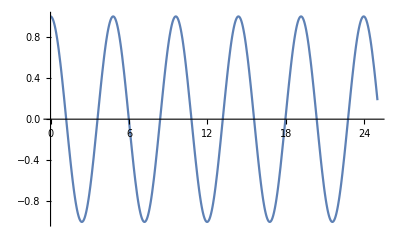

```mathematica
aproximace[t_] := poc*Cos[M*t]+poc^3/192*(Cos[3*M*t]-Cos[M*t])+((26 Cos[t *M]+Cos[3 *t*M]) Sin[t *M]^2)/9216;
Plot[aproximace[t], time]
```

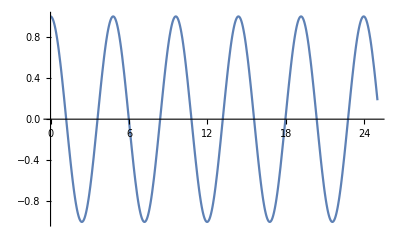

```mathematica
aprox[t_] := poc*Cos[M*t]+poc^3/192*(Cos[3*M*t]-Cos[M*t]);
Plot[aprox[t], time]
```

```mathematica
sl1=Table[aprox[t],{t, 0, 25,1}]
```

{1.,0.251026,-0.864483,-0.693485,0.502175,0.96057,-0.0170779,-0.969836,-0.472032,0.718202,0.84624,-0.284042,-0.999366,-0.21774,0.881673,0.66796,-0.531757,-0.950101,0.0512155,0.977883,0.441366,-0.742078,-0.826972,0.316752,0.997466,0.184221}

```mathematica
sl2 =Table[aproximace[t],{t, 0, 25,1}]
```

{1.,0.25163,-0.865084,-0.694451,0.503159,0.960778,-0.0171214,-0.969997,-0.472991,0.719138,0.846899,-0.284714,-0.99937,-0.218272,0.882215,0.66895,-0.532759,-0.950359,0.0513457,0.978003,0.442292,-0.742979,-0.827687,0.317486,0.99748,0.184676}

```mathematica
sl3=Table[Evaluate[y[t] /. sol], {t, 0, 25, 1}]
```

{{1.},{0.25972},{-0.875165},{-0.705212},{0.524199},{0.961383},{-0.0281047},{-0.974821},{-0.476062},{0.743075},{0.847561},{-0.313376},{-0.998554},{-0.20518},{0.900131},{0.665121},{-0.570615},{-0.945127},{0.0842176},{0.985415},{0.426352},{-0.778614},{-0.817381},{0.365974},{0.994218},{0.149941}}

```mathematica
Grid[{{"aprox","aproximace","NDSole"},{TableForm[sl1],TableForm[sl2],TableForm[sl3]}},Frame->All]
```

aprox | aproximace | NDSole
1.
0.251026
-0.864483
-0.693485
0.502175
0.96057
-0.0170779
-0.969836
-0.472032
0.718202
0.84624
-0.284042
-0.999366
-0.21774
0.881673
0.66796
-0.531757
-0.950101
0.0512155
0.977883
0.441366
-0.742078
-0.826972
0.316752
0.997466
0.184221 | 1.
0.25163
-0.865084
-0.694451
0.503159
0.960778
-0.0171214
-0.969997
-0.472991
0.719138
0.846899
-0.284714
-0.99937
-0.218272
0.882215
0.66895
-0.532759
-0.950359
0.0513457
0.978003
0.442292
-0.742979
-0.827687
0.317486
0.99748
0.184676 | 1.
0.25972
-0.875165
-0.705212
0.524199
0.961383
-0.0281047
-0.974821
-0.476062
0.743075
0.847561
-0.313376
-0.998554
-0.20518
0.900131
0.665121
-0.570615
-0.945127
0.0842176
0.985415
0.426352
-0.778614
-0.817381
0.365974
0.994218
0.149941